```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
Off[RowReduce::luc]
Off[Solve::svars]
$Assumptions={θ>0,n∈Integers,m∈Integers,j∈Integers,i∈Integers,n≥0,m≥0,j≥0,i≥0};
SetOptions[Plot,
PlotStyle->{{Red,Thick},{Purple,Thick},{Blue,Thick},{Cyan,Thick}},
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

colorlist={Blue,Red,Darker[Green],Darker[Yellow],Orange,Lighter[Green],Lighter[Brown],Purple,Cyan}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
WriteDirectory="/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files/Optimal_Error_1D_Heat";
SetDirectory[NotebookDirectory[]];
```

## Some Testing with Hermite Functions (normalized)

```mathematica
f0[c_]=1/(√(2π))Exp[-c^2/2];
fM[c_]=(c v-θ/2+(c^2 θ)/2+ρ)f0[c];
H[i_,c_]=1/(√Gamma[i+1] 2^(i/2))HermiteH[i,c/√2];

(*Distribution with respect to L2*)
H2[i_,c_]=(1 2^(1/4) (2π)^(1/4))/(√Gamma[i+1] 2^(i/2))HermiteH[i,c];
fG[c_,n_]:=∑_(k=0)^(n-1) α[k]H[k,c]f0[c];
fL2[c_,n_]:=∑_(k=0)^(n-1) α[k]H2[k,c]f0[c];

(*The following routine integrates the following expressions ∫_0^∞ H[n,c]H[m,c]f0[c]ⅆc *)
```

```mathematica
HSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(n!m!))/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];

(*Simplified expression for half space integral *)
ExplicitHSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(m!))/(√(n!))(∑_(p=1)^n 1/((p-m-2)!! (1-p+m)! (p-n-1)!!)+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];
```

### Permutation matrix

```mathematica
(*Returns a transformation matrix from var2 to var1 i.e. var1=Perm v2*)
PermuteVar[var1_,var2_]:=Module[{result,nEqn,pos},

nEqn = Length[var1];
result = ConstantArray[0,{nEqn,nEqn}];

Do[pos = Flatten[Position[var2,var1[[ii]]]];
result⟦ii,pos⟧=1,{ii,1,nEqn}];

result

]
```

## Equations for α_j, incl. Eigenvalues

(0 | 1 | 0 | 0
1 | 0 | √2 | 0
0 | √2 | 0 | √3
0 | 0 | √3 | 0)

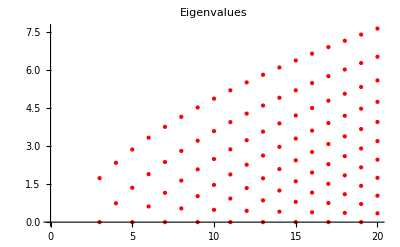

```mathematica
AA[n_]:=Table[If[i==j+1,√i,If[i==j-1,√(i+1),0]],{i,0,n-1},{j,0,n-1}]

MatrixForm[AA[4]]
ListPlot[N[Table[Thread[{Table[n,{i,1,If[OddQ[n],(n)/2+1,(n)/2]}],N[Select[Eigenvalues[AA[n]],#≥0&]]}],{n,3,20}]],PlotLabel->"Eigenvalues",PlotStyle->{{Red,Thick,PointSize[Large]}}]
```

## Boundary Matrices

```mathematica
Clear[MatBoe]
```

### Mat Aoe

```mathematica
(*construct Aoe*)
MatAoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=ConstantArray[0,{Length[IDOdd],Length[IDEven]}];
Do[Do[If[ii==jj,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧],If[jj==ii+1,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧+1]]],{jj,1,Length[IDEven]}],{ii,1,Length[IDOdd]}];

result

]
```

### Mat Boe

```mathematica
(*With the assumption that the normal points from the gas into the wall.*)
MatBoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven,rhoW},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=Flatten[ConstantArray[0,{Length[IDOdd],1}]];


(*First we compute the density at the wall*)
rhoW=Expand[ρW/.Solve[(Expand[(ρW HSpcInt[1,0]+0 HSpcInt[1,1]+θW/√2 HSpcInt[1,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[1,2j]])==0,ρW]⟦1⟧];


(*2 comes from the left hand side of the boundary conditions and the minus comes from the direction of the normal*)
Do[result⟦ii⟧=-2((rhoW HSpcInt[IDOdd⟦ii⟧,0]+0 HSpcInt[IDOdd⟦ii⟧,1]+θW/√2 HSpcInt[IDOdd⟦ii⟧,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[IDOdd⟦ii⟧,2j]),{ii,1,Length[IDOdd]}];

CoefficientArrays[result,Map[α[#]&,IDEven]]⟦2⟧
]
```

### Mat Onsager

```mathematica
MatOnsager[n_]:=Module[{Btilde,result},

Btilde=MatBoe[n]⟦1;;-1,1;;Length[MatBoe[n]]⟧;
Btilde.Inverse[MatAoe[n]⟦1;;-1,1;;Length[MatAoe[n]]⟧]
]
```

## Check Boundary Stability

### Stability Check

```mathematica
CheckBoundary[n_]:=Module[{entropy,error,numEntries,OnsagerMat},

OnsagerMat =MatOnsager[n];
error =Simplify[ OnsagerMat-Transpose[OnsagerMat]];
numEntries=Length[Flatten[OnsagerMat]];

Print[Style["Num Tensors: ",FontColor->Black],n];
Print[Style["Checking Symmetricity",FontColor->Magenta]];
If[Count[Flatten[error],0]==numEntries,Print[Style["Symmetric",FontColor->Green]],Print[Style["UnSymmetric",FontColor->Red]]];

Print[Style["Checking Eigenvalues",FontColor->Brown]];
(*equality with zero will exists because of no penetration boundary condition*)
If[Length[Select[Eigenvalues[OnsagerMat],#<0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Definite",FontColor->Green]]];

]
```

```mathematica
Ntensors = Range[4,20,1];
Do[CheckBoundary[ii],{ii,Ntensors}];
```

Num Tensors: 4

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 5

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 6

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 7

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 8

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 9

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 10

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 11

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 12

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 13

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 14

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 15

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 16

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 17

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 18

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 19

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

Num Tensors: 20

Checking Symmetricity

Symmetric

Checking Eigenvalues

Positive Definite

## Construct Boundary Conditions

### core routine

```mathematica
(*flag == 0 for unstable,flag == 1 for stable*)
ConstructStableBC[n_,flag_,Onsager_]:=Module[{BCMat,OddVar,EvenVar,IDEven,IDOdd,result,Boe},


IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];
result=Flatten[ConstantArray[0,{Length[IDOdd]-1}]];

OddVar=Map[α[#]&,IDOdd];
EvenVar=Map[α[#]&,IDEven];

If[flag==0,Boe=MatBoe[n],Boe=Onsager.MatAoe[n];];

(*we neglect the first boundary condition*)
Do[result⟦ii⟧=α[IDOdd⟦ii+1⟧]-Boe⟦ii+1,All⟧.Map[α[#]&,IDEven]+Boe⟦ii+1,2⟧/(√2)θW,{ii,1,Length[IDOdd]-1}];

Expand[Simplify[result]]
]
```

```mathematica
(*Do[bc0[ii]=ConstructStableBC[ii,0];
bc0Stable[ii]=ConstructStableBC[ii,1];,{ii,5,50}];*)
```

```mathematica
AA[5]//MatrixForm
```

(0 | 1 | 0 | 0 | 0
1 | 0 | √2 | 0 | 0
0 | √2 | 0 | √3 | 0
0 | 0 | √3 | 0 | 2
0 | 0 | 0 | 2 | 0)

```mathematica
Clear[bc]
```

### Acceptable Onsager Matrices

```mathematica
FixOnsager[OnsagerMat_]:=Module[{domain,OnsagerNew,ev,PositiveEV,commonelem},
OnsagerNew=OnsagerMat;
(*We only change the first two onsager coefficients*)

OnsagerNew⟦2,2⟧*=ζ1;
OnsagerNew⟦3,3⟧*=ζ2;

domain=Range[0.5,3,0.1];
domain=Flatten[Table[Table[{domain⟦ii⟧,domain⟦jj⟧},{jj,1,Length[domain]}],{ii,1,Length[domain]}],1];

(*list of eigenvalues corresponding to different values of the onsager coefficients*)
ev=Table[N[Eigenvalues[OnsagerNew⟦2;;-1,2;;-1⟧/.{ζ1->domain⟦ii,1⟧,ζ2->domain⟦ii,2⟧}]],{ii,1,Length[domain]}];

(*location of positive eigenvalues*)
PositiveEV=Table[Flatten[Position[ev⟦All,ii⟧,_?(#>0&)]],{ii,1,Length[ev⟦1⟧]}];
commonelem=PositiveEV⟦1⟧;
Do[commonelem=Intersection[PositiveEV⟦ii⟧,commonelem];,{ii,2,Length[PositiveEV]}];

{domain⟦commonelem⟧,ev⟦commonelem⟧,Table[OnsagerNew/.{ζ1->domain⟦commonelem⟦ii⟧,1⟧,ζ2->domain⟦commonelem⟦ii⟧,2⟧},{ii,1,Length[commonelem]}]}
]
```

### Test Range of Positivity

```mathematica
positiveEV=Table[FixOnsager[MatOnsager[ii]]⟦2⟧,{ii,7,23,2}];
```

```mathematica
Do[If[Length[Flatten[Position[positiveEV⟦ii⟧,_?(#<0&)]]]>0,Print[Style["Not Passed",FontColor->Red]],Print[Style["Passed",FontColor->Green]]];,{ii,1,Length[positiveEV]}]
```

Passed

Passed

Passed

«6 more identical outputs»

### OnsagerMatrices

```mathematica
min=6;
max=20;
```

```mathematica
(*The original onsager coefficients*)
Do[onsagerOld[ii]=MatOnsager[ii],{ii,min,max}];
```

```mathematica
(*onsager matrices which have positivity and symmetricity*)
Do[{onsagercoeff[ii],onsagerNew[ii]}=FixOnsager[onsagerOld[ii]]⟦{1,-1}⟧,{ii,min,max}];
```

### Boundary Conditions

```mathematica
Do[bcPBCOptimal[ii]=Table[ConstructStableBC[ii,onsagerNew[ii]⟦jj⟧],{jj,1,Length[onsagerNew[ii]]}],{ii,min,max}];

Do[bcMBC[ii]=ConstructStableBC[ii,0,onsagerOld[ii]],{ii,min,max}];

Do[bcPBC[ii]=ConstructStableBC[ii,1,onsagerOld[ii]],{ii,min,max}];
```

## Solving Routines

### returns the solution

```mathematica
Clear[nvar,kn,thetaw,A0,P0,λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC]

(*flag = 0 for unstable, flag == 1 for stable*)
GetSolution[nvar_,kn_,thetaw_,flag_,bcinput_]:=Block[{λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc},
A0=AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{λ0,vv}=Eigensystem[{P0,1.0A0}];
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,λ}],1]];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];
λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];
B0⟦1⟧=0;
alpha=0;

coef[0,4]=Kn k[0]; (* heat flux constant*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,1}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,1}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+alpha B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}];

solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];
res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];


bc=bcinput;

bcEqn=Table[bc⟦i⟧,{i,1,nvar/2-1}]/.res/.{x->1/2}/.{β1->√(π/2)(2-χ)/(2χ)}/.{χ->1};

solBC=Solve[Thread[(bcEqn/.{Kn->kn,θW->thetaw})==0],Table[k[i],{i,0,nvar/2-2}]]⟦1⟧;

(*Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}*)
{{√2. α[2],√6. α[3]}/.res/.solBC/.{Kn->kn},Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}}
]
```

```mathematica
(*u[x_]=GetSolution[4,0.1,1.0]
Chop[Expand[N[A0.u'[x]-1/Kn P0.u[x]]/.{Kn->0.1}]]
*)
```

### returns the distribution function

```mathematica
(*flag = 0 for unstable, flag == 1 for stable*)
Getf[nvar_,kn_,thetaw_,flag_]:=Block[{λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc0,result},
A0=AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{λ0,vv}=Eigensystem[{P0,1.0A0}];
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,λ}],1]];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];
λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];
B0⟦1⟧=0;
alpha=0;

coef[0,4]=Kn k[0]; (* heat flux constant*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,1}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,1}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+alpha B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}];

solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];
res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];


If[flag==0,bc0=ConstructStableBC[nvar,0],bc0=ConstructStableBC[nvar,1]];

bcEqn=Table[bc0⟦i⟧,{i,1,nvar/2-1}]/.res/.{x->1/2}/.{β1->√(π/2)(2-χ)/(2χ)}/.{χ->1};

solBC=Solve[Thread[(bcEqn/.{Kn->kn,θW->thetaw})==0],Table[k[i],{i,0,nvar/2-2}]]⟦1⟧;

(*Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}*)

res/.solBC/.{Kn->kn}
]
```

## Discrete Velocity Solution

```mathematica
Arrayθ[gaussloc_,gaussW_]:=Table[gaussW⟦ii⟧(gaussloc⟦ii⟧^2-1),{ii,1,Length[gaussW]}];
```

### Kn 0.1

```mathematica
exactfKn0p1=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results_Discrete_Velocity/1D_Heat_Conduction/Kn0p1/fx24c200.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn0p1=exactfKn0p1⟦1,IDpointsc⟧;
pointsxKn0p1=exactfKn0p1⟦1,IDpointsx⟧;
θKn0p1=Interpolation[Table[{exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1;;pointscKn0p1*(ii-1)+IDdata+pointscKn0p1,2⟧,exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1;;pointscKn0p1*(ii-1)+IDdata+pointscKn0p1,3⟧].exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+1;;pointscKn0p1*(ii-1)+IDdata+pointscKn0p1,4⟧},{ii,1,pointsxKn0p1}],InterpolationOrder->3];

fKn0p1=Table[Interpolation[Table[{exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+jj,2⟧,exactfKn0p1⟦pointscKn0p1*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn0p1}],InterpolationOrder->3],{ii,1,pointsxKn0p1}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

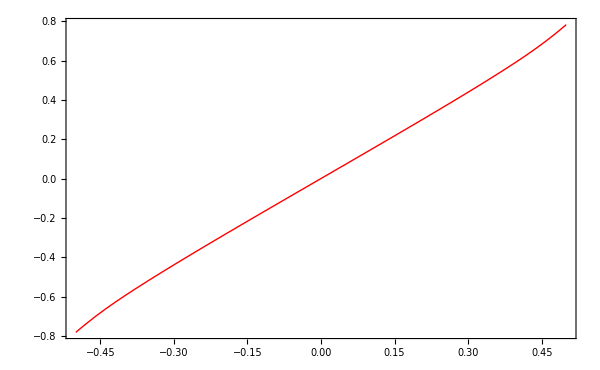

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

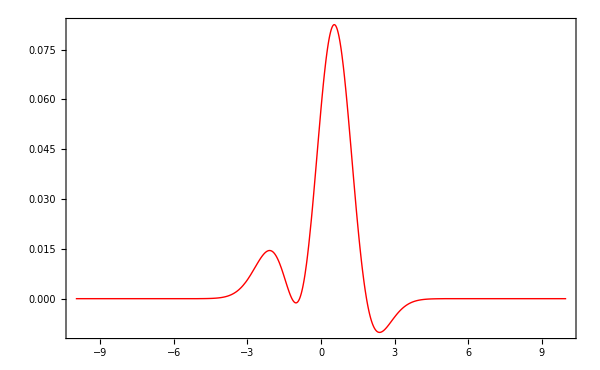

```mathematica
Plot[{θKn0p1[x]},{x,-0.5,0.5}]
Plot[{fKn0p1⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### Kn 1.0

```mathematica
exactfKn1p0=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results_Discrete_Velocity/1D_Heat_Conduction/Kn1p0/fx24c200.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn1p0=exactfKn1p0⟦1,IDpointsc⟧;
pointsxKn1p0=exactfKn1p0⟦1,IDpointsx⟧;
θKn1p0=Interpolation[Table[{exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+1;;pointscKn1p0*(ii-1)+IDdata+pointscKn1p0,2⟧,exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+1;;pointscKn1p0*(ii-1)+IDdata+pointscKn1p0,3⟧].exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+1;;pointscKn1p0*(ii-1)+IDdata+pointscKn1p0,4⟧},{ii,1,pointsxKn1p0}],InterpolationOrder->3];

fKn1p0=Table[Interpolation[Table[{exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+jj,2⟧,exactfKn1p0⟦pointscKn1p0*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn1p0}],InterpolationOrder->3],{ii,1,pointsxKn1p0}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

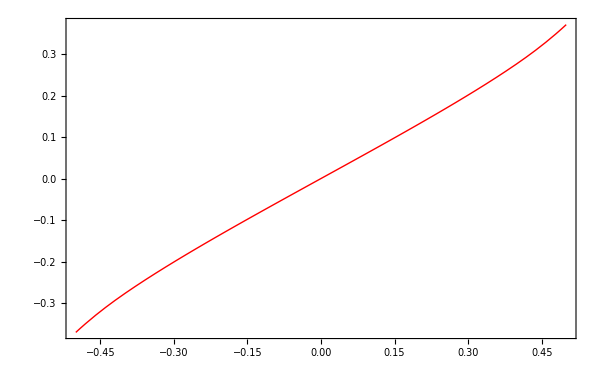

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

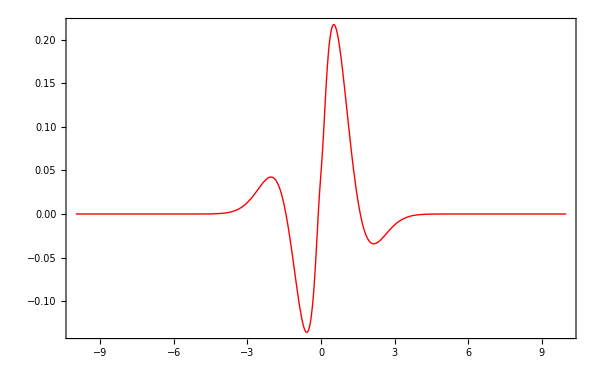

```mathematica
Plot[{θKn1p0[x]},{x,-0.5,0.5}]
Plot[{fKn1p0⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### Kn 10.0

```mathematica
exactfKn10p0=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results_Discrete_Velocity/1D_Heat_Conduction/Kn10p0/fx24c200.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn10p0=exactfKn10p0⟦1,IDpointsc⟧;
pointsxKn10p0=exactfKn10p0⟦1,IDpointsx⟧;
θKn10p0=Interpolation[Table[{exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+1;;pointscKn10p0*(ii-1)+IDdata+pointscKn10p0,2⟧,exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+1;;pointscKn10p0*(ii-1)+IDdata+pointscKn10p0,3⟧].exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+1;;pointscKn10p0*(ii-1)+IDdata+pointscKn10p0,4⟧},{ii,1,pointsxKn10p0}],InterpolationOrder->3];

fKn10p0=Table[Interpolation[Table[{exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+jj,2⟧,exactfKn10p0⟦pointscKn10p0*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn10p0}],InterpolationOrder->3],{ii,1,pointsxKn10p0}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

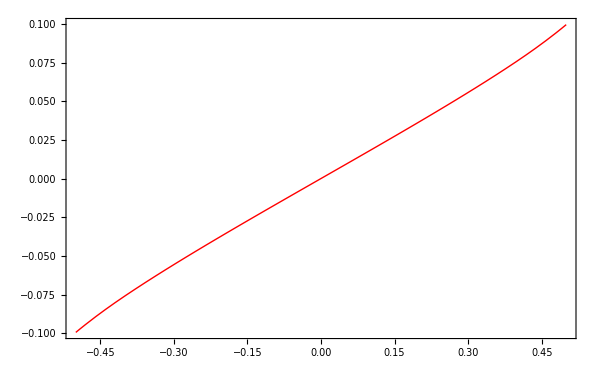

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

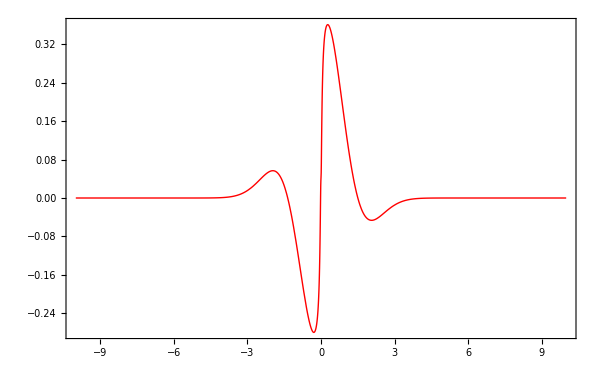

```mathematica
Plot[{θKn10p0[x]},{x,-0.5,0.5}]
Plot[{fKn10p0⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### Kn 100.0

```mathematica
exactfKn100p0=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results_Discrete_Velocity/1D_Heat_Conduction/Kn100p0/fx24c200.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn100p0=exactfKn100p0⟦1,IDpointsc⟧;
pointsxKn100p0=exactfKn100p0⟦1,IDpointsx⟧;
θKn100p0=Interpolation[Table[{exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+1;;pointscKn100p0*(ii-1)+IDdata+pointscKn100p0,2⟧,exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+1;;pointscKn100p0*(ii-1)+IDdata+pointscKn100p0,3⟧].exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+1;;pointscKn100p0*(ii-1)+IDdata+pointscKn100p0,4⟧},{ii,1,pointsxKn100p0}],InterpolationOrder->3];

fKn100p0=Table[Interpolation[Table[{exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+jj,2⟧,exactfKn100p0⟦pointscKn100p0*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn100p0}],InterpolationOrder->3],{ii,1,pointsxKn100p0}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

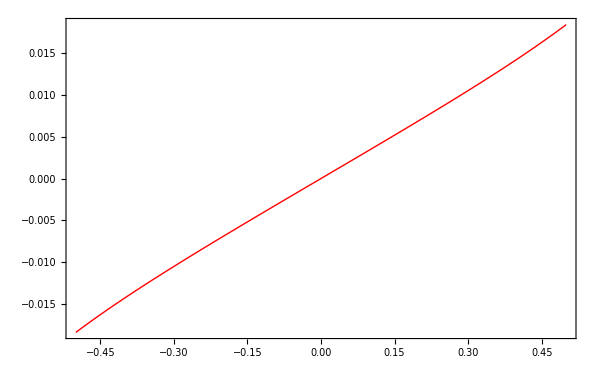

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

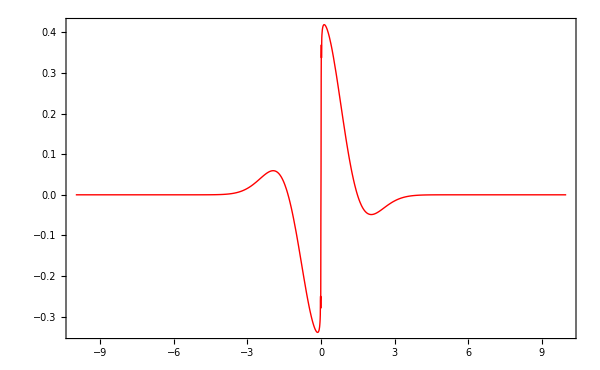

```mathematica
Plot[{θKn100p0[x]},{x,-0.5,0.5}]
Plot[{fKn100p0⟦12⟧[x]},{x,-10,10},PlotRange->Full]
```

### Kn ∞

```mathematica
exactfKn∞=Import["/Users/neerajsarna/sciebo/DG_moments_deal/Results_Discrete_Velocity/1D_Heat_Conduction/Kninf/fx9c160.dat","Table"];

IDpointsx=3;
IDpointsc=6;
IDdata=3;
pointscKn∞=exactfKn∞⟦1,IDpointsc⟧;
pointsxKn∞=exactfKn∞⟦1,IDpointsx⟧;
θKn∞=Interpolation[Table[{exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+1,1⟧-0.5,Arrayθ[exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+1;;pointscKn∞*(ii-1)+IDdata+pointscKn∞,2⟧,exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+1;;pointscKn∞*(ii-1)+IDdata+pointscKn∞,3⟧].exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+1;;pointscKn∞*(ii-1)+IDdata+pointscKn∞,4⟧},{ii,1,pointsxKn∞}],InterpolationOrder->3];

fKn∞=Table[Interpolation[Table[{exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+jj,2⟧,exactfKn∞⟦pointscKn∞*(ii-1)+IDdata+jj,4⟧},{jj,1,pointscKn∞}],InterpolationOrder->3],{ii,1,pointsxKn∞}];
```

InterpolatingFunction::dmval: Input value {-0.49998} lies outside the range of data in the interpolating function. Extrapolation will be used.

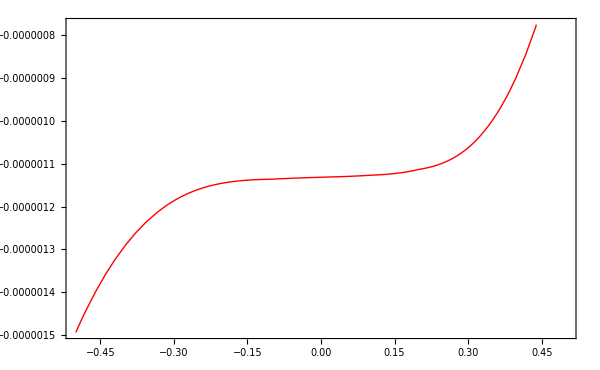

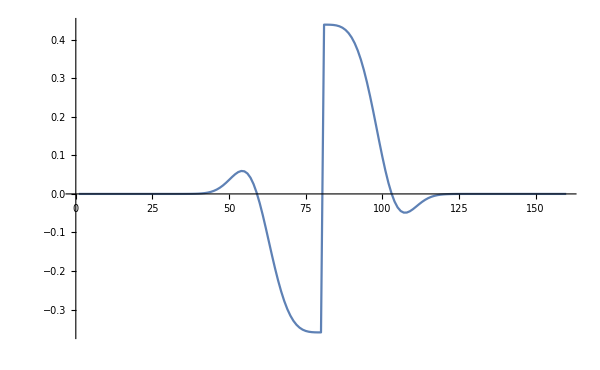

```mathematica
Plot[{Chop[θKn∞[x],10^-7]},{x,-0.5,0.5}]
ListPlot[exactfKn∞⟦IDdata+1;;IDdata+pointscKn∞,4⟧,PlotRange->Full,Joined->True]
```

## Return Error

```mathematica
(*Returns the error. Flag == 0 for MBC, Flag == 1 for PBC and Flag == 2 for PBCOptimal*)
ReturnError[nvar_,Kn_,flag_]:=Module[{onsagerMat,bc,solution,error,numsolutions,time1,time2,gaussx,gaussW,domain},

If[nvar <min || nvar >max,Print[Style["Variables beyond present theory",FontColor->Red]]];

Which[flag==0,
bc={bcMBC[nvar]};,
flag==1,
bc={bcPBC[nvar]};,
flag==2,
bc=bcPBCOptimal[nvar];];

numsolutions=Length[bc];

time1=AbsoluteTiming[Do[
solution[ii][x_]=GetSolution[nvar,Kn,1.0,1,bc⟦ii⟧]⟦1,1⟧;,{ii,1,numsolutions}]];

gaussx=GaussianQuadratureWeights[10,-0.5,0.5]⟦All,1⟧;
gaussW=GaussianQuadratureWeights[10,-0.5,0.5]⟦All,2⟧;

time2=AbsoluteTiming[Which[Kn==0.1,
error=Table[Sum[gaussW⟦jj⟧Abs[(solution[ii][x]/.{x->gaussx⟦jj⟧})-θKn0p1[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,1,numsolutions}];,
Kn==1.0,
error=Table[Sum[gaussW⟦jj⟧Abs[(solution[ii][x]/.{x->gaussx⟦jj⟧})-θKn1p0[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,1,numsolutions}];,
Kn==10.0,
error=Table[Sum[gaussW⟦jj⟧Abs[(solution[ii][x]/.{x->gaussx⟦jj⟧})-θKn10p0[gaussx⟦jj⟧]],{jj,1,Length[gaussx]}],{ii,1,numsolutions}];
]];

Print["Time in solving ",time1];
Print["Time in error computation ",time2];
{Flatten[Position[error,Min[error]]],Min[error],error}

]
```

## Results

### Writting routine

```mathematica
WriteError[result_,filename_,Ntensors_]:=Module[{str},

str=OpenWrite[StringJoin[WriteDirectory,"/",filename,ToString[Ntensors],".dat"]];

(*Write the number of tensors and the optimal error value*)
WriteString[str," Tensors ",ToString[Ntensors]," Optimal Error ",result⟦2⟧,"\n"];
WriteString[str," #error","\n"];

Do[WriteString[str,ToString[result⟦3⟧⟦ii⟧],"\n"];,{ii,1,Length[result⟦3⟧]}];

Close[str];
]
```

### MBC

#### Kn = 0.1

```mathematica
Do[resultMBCKn0p1[ii]=ReturnError[ii,0.1,0]⟦-2⟧,{ii,min,max}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

Time in solving {0.00584,Null}

Time in error computation {0.0525,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {0.00632,Null}

Time in error computation {0.04484,Null}

Time in solving {0.01012,Null}

Time in error computation {0.00032,Null}

Time in solving {0.01167,Null}

Time in error computation {0.00034,Null}

Time in solving {0.01738,Null}

Time in error computation {0.00041,Null}

Time in solving {0.01805,Null}

Time in error computation {0.0004,Null}

Time in solving {0.02659,Null}

Time in error computation {0.0005,Null}

Time in solving {0.02949,Null}

Time in error computation {0.00049,Null}

Time in solving {0.04216,Null}

Time in error computation {0.00057,Null}

Time in solving {0.04465,Null}

Time in error computation {0.00057,Null}

Time in solving {0.05996,Null}

Time in error computation {0.00073,Null}

Time in solving {0.06685,Null}

Time in error computation {0.00072,Null}

Time in solving {0.08416,Null}

Time in error computation {0.00073,Null}

Time in solving {0.09221,Null}

Time in error computation {0.00081,Null}

Time in solving {0.11362,Null}

Time in error computation {0.0009,Null}

#### Kn = 1.0

```mathematica
Do[resultMBCKn1p0[ii]=ReturnError[ii,1,0]⟦-2⟧,{ii,min,max}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

Time in solving {0.00596,Null}

Time in error computation {0.05753,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {0.00623,Null}

Time in error computation {0.04735,Null}

Time in solving {0.011,Null}

Time in error computation {0.00032,Null}

Time in solving {0.01323,Null}

Time in error computation {0.00044,Null}

Time in solving {0.01702,Null}

Time in error computation {0.0004,Null}

Time in solving {0.02044,Null}

Time in error computation {0.00041,Null}

Time in solving {0.02634,Null}

Time in error computation {0.00049,Null}

Time in solving {0.03088,Null}

Time in error computation {0.00048,Null}

Time in solving {0.04096,Null}

Time in error computation {0.00058,Null}

Time in solving {0.04624,Null}

Time in error computation {0.00061,Null}

Time in solving {0.06517,Null}

Time in error computation {0.00073,Null}

Time in solving {0.07001,Null}

Time in error computation {0.00066,Null}

Time in solving {0.08538,Null}

Time in error computation {0.00073,Null}

Time in solving {0.09533,Null}

Time in error computation {0.00073,Null}

Time in solving {0.12438,Null}

Time in error computation {0.00086,Null}

#### Kn = 10.0

```mathematica
Do[resultMBCKn10p0[ii][x_]=ReturnError[ii,10.0,0]⟦-2⟧,{ii,min,max}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

Time in solving {0.00807,Null}

Time in error computation {0.04874,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {0.00698,Null}

Time in error computation {0.05103,Null}

Time in solving {0.01516,Null}

Time in error computation {0.00042,Null}

Time in solving {0.01062,Null}

Time in error computation {0.00031,Null}

Time in solving {0.01784,Null}

Time in error computation {0.00041,Null}

Time in solving {0.01962,Null}

Time in error computation {0.0004,Null}

Time in solving {0.02639,Null}

Time in error computation {0.00047,Null}

Time in solving {0.03067,Null}

Time in error computation {0.00075,Null}

Time in solving {0.05203,Null}

Time in error computation {0.00057,Null}

Time in solving {0.04685,Null}

Time in error computation {0.00057,Null}

Time in solving {0.05866,Null}

Time in error computation {0.00064,Null}

Time in solving {0.06543,Null}

Time in error computation {0.00074,Null}

Time in solving {0.09019,Null}

Time in error computation {0.00073,Null}

Time in solving {0.0898,Null}

Time in error computation {0.00073,Null}

Time in solving {0.11151,Null}

Time in error computation {0.0008,Null}

### PBC

#### Kn = 0.1

```mathematica
Do[resultPBCKn0p1[ii]=ReturnError[ii,0.1,1]⟦-2⟧,{ii,min,max}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

Time in solving {0.00536,Null}

Time in error computation {0.0495,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {0.00678,Null}

Time in error computation {0.04974,Null}

Time in solving {0.01052,Null}

Time in error computation {0.00035,Null}

Time in solving {0.01145,Null}

Time in error computation {0.00032,Null}

Time in solving {0.01685,Null}

Time in error computation {0.0004,Null}

Time in solving {0.01992,Null}

Time in error computation {0.00042,Null}

Time in solving {0.0265,Null}

Time in error computation {0.00049,Null}

Time in solving {0.02809,Null}

Time in error computation {0.00048,Null}

Time in solving {0.04161,Null}

Time in error computation {0.00057,Null}

Time in solving {0.04615,Null}

Time in error computation {0.00058,Null}

Time in solving {0.05709,Null}

Time in error computation {0.00067,Null}

Time in solving {0.06969,Null}

Time in error computation {0.000997,Null}

Time in solving {0.08384,Null}

Time in error computation {0.00073,Null}

Time in solving {0.09384,Null}

Time in error computation {0.00077,Null}

Time in solving {0.1116,Null}

Time in error computation {0.00084,Null}

#### Kn = 1.0

```mathematica
Do[resultPBCKn1p0[ii]=ReturnError[ii,1,1]⟦-2⟧,{ii,min,max}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

Time in solving {0.00822,Null}

Time in error computation {0.05251,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {0.00728,Null}

Time in error computation {0.04585,Null}

Time in solving {0.01034,Null}

Time in error computation {0.00033,Null}

Time in solving {0.01485,Null}

Time in error computation {0.00032,Null}

Time in solving {0.01695,Null}

Time in error computation {0.00053,Null}

Time in solving {0.02032,Null}

Time in error computation {0.0004,Null}

Time in solving {0.03085,Null}

Time in error computation {0.00056,Null}

Time in solving {0.02875,Null}

Time in error computation {0.00053,Null}

Time in solving {0.04534,Null}

Time in error computation {0.00056,Null}

Time in solving {0.04804,Null}

Time in error computation {0.00055,Null}

Time in solving {0.06354,Null}

Time in error computation {0.00067,Null}

Time in solving {0.07576,Null}

Time in error computation {0.00064,Null}

Time in solving {0.09057,Null}

Time in error computation {0.00074,Null}

Time in solving {0.09422,Null}

Time in error computation {0.00121,Null}

Time in solving {0.12102,Null}

Time in error computation {0.00081,Null}

#### Kn = 10.0

```mathematica
Do[resultPBCKn10p0[ii][x_]=ReturnError[ii,10.0,1]⟦-2⟧,{ii,min,max}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

Time in solving {0.00601,Null}

Time in error computation {0.04895,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {0.00748,Null}

Time in error computation {0.04475,Null}

Time in solving {0.01031,Null}

Time in error computation {0.00032,Null}

Time in solving {0.01173,Null}

Time in error computation {0.00032,Null}

Time in solving {0.01732,Null}

Time in error computation {0.0004,Null}

Time in solving {0.01846,Null}

Time in error computation {0.0004,Null}

Time in solving {0.02584,Null}

Time in error computation {0.00048,Null}

Time in solving {0.02885,Null}

Time in error computation {0.00048,Null}

Time in solving {0.04542,Null}

Time in error computation {0.00056,Null}

Time in solving {0.04633,Null}

Time in error computation {0.00057,Null}

Time in solving {0.06245,Null}

Time in error computation {0.00075,Null}

Time in solving {0.06721,Null}

Time in error computation {0.00064,Null}

Time in solving {0.08668,Null}

Time in error computation {0.00072,Null}

Time in solving {0.09257,Null}

Time in error computation {0.00079,Null}

Time in solving {0.12521,Null}

Time in error computation {0.00082,Null}

### PBC Optimal

#### Kn = 0.1

```mathematica
Do[resultPBCOptKn0p1[ii]=ReturnError[ii,0.1,2],{ii,min,max}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {3.62387,Null}

Time in error computation {0.68119,Null}

Time in solving {4.19972,Null}

Time in error computation {0.5384,Null}

Time in solving {6.35226,Null}

Time in error computation {0.61004,Null}

Time in solving {7.44122,Null}

Time in error computation {0.65436,Null}

Time in solving {10.132,Null}

Time in error computation {0.6677,Null}

Time in solving {15.97201,Null}

Time in error computation {0.85446,Null}

Time in solving {19.95227,Null}

Time in error computation {0.84488,Null}

Time in solving {19.43213,Null}

Time in error computation {0.7903,Null}

Time in solving {27.57587,Null}

Time in error computation {0.89521,Null}

Time in solving {29.84199,Null}

Time in error computation {0.88323,Null}

Time in solving {40.54006,Null}

Time in error computation {1.03239,Null}

Time in solving {44.45661,Null}

Time in error computation {0.957482,Null}

Time in solving {57.20183,Null}

Time in error computation {1.04923,Null}

Time in solving {61.88584,Null}

Time in error computation {1.14838,Null}

Time in solving {78.66925,Null}

Time in error computation {1.20487,Null}

#### Kn = 1.0

```mathematica
Do[resultPBCOptKn1p0[ii]=ReturnError[ii,1,2],{ii,min,max}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {3.7416,Null}

Time in error computation {0.79489,Null}

Time in solving {4.57,Null}

Time in error computation {0.58541,Null}

Time in solving {6.50242,Null}

Time in error computation {0.64389,Null}

Time in solving {7.79612,Null}

Time in error computation {0.691,Null}

Time in solving {11.12401,Null}

Time in error computation {0.72475,Null}

Time in solving {12.56184,Null}

Time in error computation {0.75591,Null}

Time in solving {17.55988,Null}

Time in error computation {0.80832,Null}

Time in solving {19.6123,Null}

Time in error computation {0.79522,Null}

Time in solving {27.37746,Null}

Time in error computation {0.88579,Null}

Time in solving {30.69992,Null}

Time in error computation {0.89406,Null}

Time in solving {42.27193,Null}

Time in error computation {0.979729,Null}

Time in solving {44.86483,Null}

Time in error computation {0.958903,Null}

Time in solving {57.59351,Null}

Time in error computation {1.05459,Null}

Time in solving {61.62964,Null}

Time in error computation {1.05097,Null}

Time in solving {78.81039,Null}

Time in error computation {1.09647,Null}

#### Kn = 10.0

```mathematica
Do[resultPBCOptKn10p0[ii][x_]=ReturnError[ii,10.0,2],{ii,min,max}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {3.49546,Null}

Time in error computation {0.78122,Null}

Time in solving {4.48797,Null}

Time in error computation {0.62718,Null}

Time in solving {6.56884,Null}

Time in error computation {0.67813,Null}

Time in solving {7.3492,Null}

Time in error computation {0.65288,Null}

Time in solving {10.68856,Null}

Time in error computation {0.73713,Null}

Time in solving {12.33527,Null}

Time in error computation {0.74999,Null}

Time in solving {17.29741,Null}

Time in error computation {0.82915,Null}

Time in solving {19.52142,Null}

Time in error computation {0.83517,Null}

Time in solving {27.60645,Null}

Time in error computation {0.8847,Null}

Time in solving {28.92197,Null}

Time in error computation {0.86209,Null}

Time in solving {40.1966,Null}

Time in error computation {0.90683,Null}

Time in solving {42.74708,Null}

Time in error computation {0.92528,Null}

Time in solving {57.07247,Null}

Time in error computation {0.979918,Null}

Time in solving {68.11504,Null}

Time in error computation {0.9477,Null}

Time in solving {79.80366,Null}

Time in error computation {2.20989,Null}

### Plots

#### Kn = 0.1

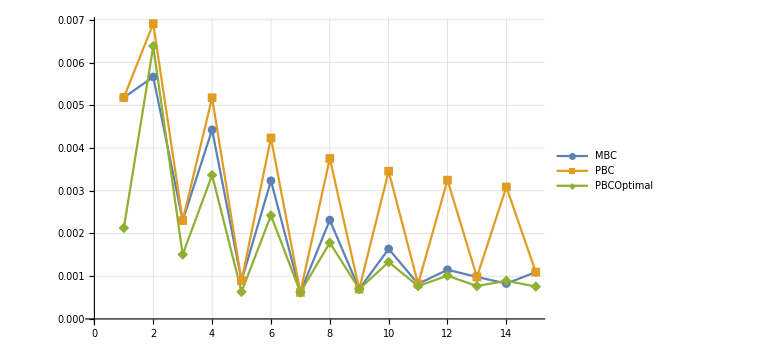

```mathematica
ListPlot[{Table[resultMBCKn0p1[ii],{ii,min,max}],Table[resultPBCKn0p1[ii],{ii,min,max}],Table[resultPBCOptKn0p1[ii]⟦2⟧,{ii,min,max}]},Joined->True,PlotLegends->{"MBC","PBC","PBCOptimal"},GridLines->Automatic,PlotMarkers->Automatic,ImageSize->Large]
```

#### Kn = 1.0

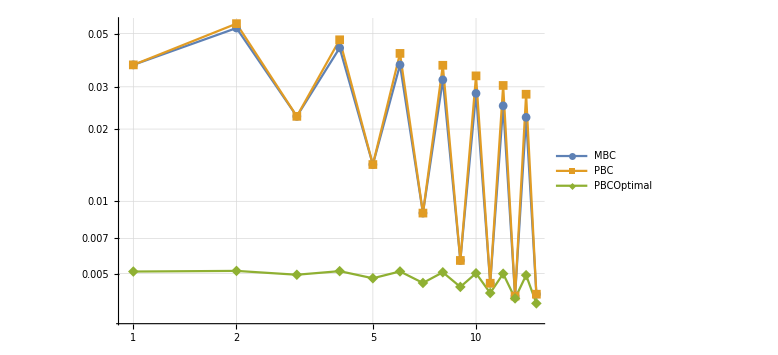

```mathematica
ListLogLogPlot[{Table[resultMBCKn1p0[ii],{ii,min,max}],Table[resultPBCKn1p0[ii],{ii,min,max}],Table[resultPBCOptKn1p0[ii]⟦2⟧,{ii,min,max}]},Joined->True,PlotLegends->{"MBC","PBC","PBCOptimal"},GridLines->Automatic,PlotMarkers->Automatic,ImageSize->Large]
```

#### Kn = 10.0

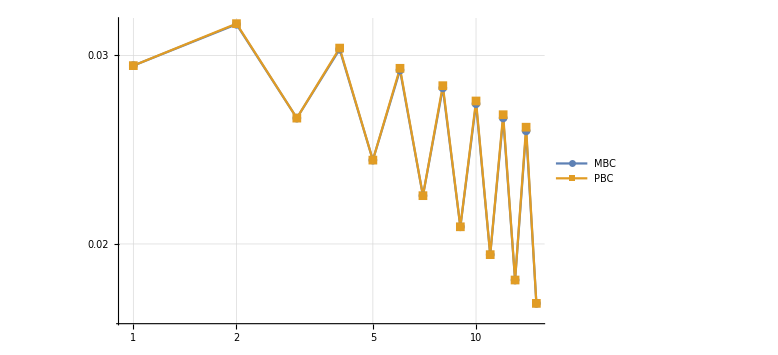

```mathematica
ListLogLogPlot[{Table[resultMBCKn10p0[ii][x],{ii,min,max}],Table[resultPBCKn10p0[ii][x],{ii,min,max}](*,Table[resultPBCOptKn10p0[ii][x]⟦2⟧,{ii,min,max}]*)},Joined->True,PlotLegends->{"MBC","PBC","PBCOptimal"},GridLines->Automatic,PlotMarkers->Automatic,ImageSize->Large]
```

### Error variation for different theories

#### Ntensors = 7

```mathematica
error7Kn0p1=ReturnError[7,0.1,2]⟦-1⟧;
error7Kn1p0=ReturnError[7,1.0,2]⟦-1⟧;
error7Kn10p0=ReturnError[7,10.0,2]⟦-1⟧;
error7Kn0p1=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error7Kn0p1⟦ii⟧}],{ii,1,Length[error7Kn0p1]}];
error7Kn1p0=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error7Kn1p0⟦ii⟧}],{ii,1,Length[error7Kn1p0]}];
error7Kn10p0=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error7Kn10p0⟦ii⟧}],{ii,1,Length[error7Kn10p0]}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {4.11116,Null}

Time in error computation {0.6499,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {4.30056,Null}

Time in error computation {0.78213,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {4.31841,Null}

Time in error computation {0.66279,Null}

```mathematica
ListPlot3D[error7Kn0p1]
ListPlot3D[error7Kn1p0]
ListPlot3D[error7Kn10p0]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

#### Ntensors = 8

```mathematica
error8Kn0p1=ReturnError[8,0.1,2]⟦-1⟧;
error8Kn1p0=ReturnError[8,1.0,2]⟦-1⟧;
error8Kn10p0=ReturnError[8,10.0,2]⟦-1⟧;
error8Kn0p1=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error8Kn0p1⟦ii⟧}],{ii,1,Length[error8Kn0p1]}];
error8Kn1p0=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error8Kn1p0⟦ii⟧}],{ii,1,Length[error8Kn1p0]}];
error8Kn10p0=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error8Kn10p0⟦ii⟧}],{ii,1,Length[error8Kn10p0]}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {6.31555,Null}

Time in error computation {0.72682,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {6.20566,Null}

Time in error computation {0.72142,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {6.17609,Null}

Time in error computation {0.70443,Null}

```mathematica
ListPlot3D[error8Kn0p1]
ListPlot3D[error8Kn1p0]
ListPlot3D[error8Kn10p0]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

#### Ntensors = 9

```mathematica
error9Kn0p1=ReturnError[9,0.1,2]⟦-1⟧;
error9Kn1p0=ReturnError[9,1.0,2]⟦-1⟧;
error9Kn10p0=ReturnError[9,10.0,2]⟦-1⟧;
error9Kn0p1=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error9Kn0p1⟦ii⟧}],{ii,1,Length[error9Kn0p1]}];
error9Kn1p0=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error9Kn1p0⟦ii⟧}],{ii,1,Length[error9Kn1p0]}];
error9Kn10p0=Table[Flatten[{onsagercoeff[7]⟦ii⟧,error9Kn10p0⟦ii⟧}],{ii,1,Length[error9Kn10p0]}];
```

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {7.472,Null}

Time in error computation {0.751,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {7.31988,Null}

Time in error computation {0.71083,Null}

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.486953} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Time in solving {7.29556,Null}

Time in error computation {0.71168,Null}

```mathematica
ListPlot3D[error9Kn0p1]
ListPlot3D[error9Kn1p0]
ListPlot3D[error9Kn10p0]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

### Value Optimal Onsager Coefficients

```mathematica
OptimalCoeffsKn0p1=Table[onsagercoeff[ii]⟦resultPBCOptKn0p1[ii]⟦1⟧⟧,{ii,min,max}];
OptimalCoeffsKn1p0=Table[onsagercoeff[ii]⟦resultPBCOptKn1p0[ii]⟦1⟧⟧,{ii,min,max}];
OptimalCoeffsKn10p0=Table[onsagercoeff[ii]⟦resultPBCOptKn10p0[ii]⟦1⟧⟧,{ii,min,max}];
```

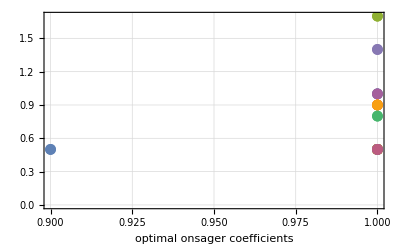

```mathematica
ListPlot[OptimalCoeffsKn0p1,GridLines->Automatic,Frame->True,FrameLabel->{"optimal onsager coefficients"}]
```

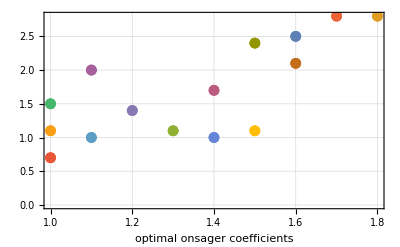

```mathematica
ListPlot[OptimalCoeffsKn1p0,GridLines->Automatic,Frame->True,FrameLabel->{"optimal onsager coefficients"}]
```

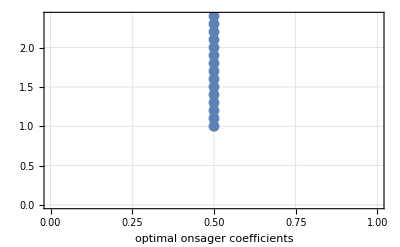

```mathematica
ListPlot[OptimalCoeffsKn10p0,GridLines->Automatic,Frame->True,FrameLabel->{"optimal onsager coefficients"}]
```

### Write Optimal error and Onsager Coefficients

#### Kn = 0.1

```mathematica
Do[WriteError[resultPBCOptKn0p1[ii],"Kn0p1/OptimalError",ii],{ii,min,max}];
```

#### Kn = 1.0

```mathematica
Do[WriteError[resultPBCOptKn1p0[ii],"Kn1p0/OptimalError",ii],{ii,min,max}];
```

#### Kn = 10.0

```mathematica
Do[WriteError[resultPBCOptKn10p0[ii][x],"Kn10p0/OptimalError",ii],{ii,min,max}];
```

## Proof for onsager

### Inv Aoe

```mathematica
γ[i_]:=(-√(2i))/(√(2i-1));
f[i_]:=1/(√(2i-1));

(*Product from zero to omega so omega + 1 terms*)
Productγ[i_,ω_]:=Product[γ[ii],{ii,i,i+ω}];

SimplifiedProductγ[i_,ω_]:=(-1)^(ω+1)If[i>1,√(((2i+2ω)!!(2i-3)!!)/((2i-2)!!(2i+2ω-1)!!)),√(((2i+2ω)!!)/((2i-2)!!(2i+2ω-1)!!))];
```

```mathematica
ExplicitInvAoe[nvar_]:=Module[{result,entries},
entries=Length[MatAoe[nvar]];
result=IdentityMatrix[entries];

(*fill upper triangle of result*)
Do[result⟦ii,ii⟧=1/(√(2ii-1));

Do[result⟦ii,ii+r⟧=Productγ[ii,r-1]f[ii+r];,{r,1,entries-ii}];
;,{ii,1,entries}];

result
]
```

```mathematica
Product[γ[i],{i,1,1}]
```

-√2

```mathematica
ExplicitInvAoe[7]//MatrixForm
```

(1 | -√(2/3) | 2 √(2/15)
0 | 1/(√3) | -2/(√15)
0 | 0 | 1/(√5))

```mathematica
?Product
```

Product[f,{i,i_max}] evaluates the product ∏_(i=1)^i_max f. 
Product[f,{i,i_min,i_max}] starts with i=i_min. 
Product[f,{i,i_min,i_max,di}] uses steps di. 
Product[f,{i,{i_1,i_2,…}}] uses successive values i_1, i_2, ….
Product[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple product ∏_(i=i_min)^i_max ∏_(j=j_min)^j_max … f. 
Product[f,i] gives the indefinite product ∏_i f.

### Test Inv Aoe and Product Gamma

```mathematica
Do[Do[result=Simplify[Productγ[ii,jj]-SimplifiedProductγ[ii,jj]];
If[result≠0,Print[Style["Not Passed",FontColor->Red]],Print[Style["Passed",FontColor->Green]]];,{ii,1,10}],{jj,1,10}]
```

```mathematica
Do[result=ExplicitInvAoe[ii];
result=MatAoe[ii]⟦1;;-1,1;;Length[MatAoe[ii]]⟧.result;
If[Norm[result-IdentityMatrix[Length[result]]]≠0,Print[Style["Incorrect Inverse",FontColor->Red]],Print[Style["Correct Inverse",FontColor->Green]]];,{ii,7,20}]
```

Correct Inverse

Correct Inverse

Correct Inverse

«11 more identical outputs»

### Boe

```mathematica
(*Explicit formulae for matrix Boe*)
ExplicitBoe[n_]:=Module[{IDEven,IDOdd,result},

IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=ConstantArray[0,{Length[IDOdd],Length[IDEven]}];

Do[Do[result⟦ii,jj⟧=2(HSpcInt[IDOdd⟦ii⟧,IDEven⟦jj⟧]-(HSpcInt[1,IDEven⟦jj⟧]HSpcInt[IDOdd⟦ii⟧,0])/HSpcInt[1,0]),{jj,1,Length[IDEven]}];,{ii,1,Length[IDOdd]}];

result
]

(*Part one of Boe*)
ExplicitBoe1[n_]:=Module[{IDEven,IDOdd,result},

IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=ConstantArray[0,{Length[IDOdd],Length[IDEven]}];

Do[Do[result⟦ii,jj⟧=2(HSpcInt[IDOdd⟦ii⟧,IDEven⟦jj⟧]),{jj,1,Length[IDEven]}];,{ii,1,Length[IDOdd]}];

result
]

(*Part two of Boe*)
ExplicitBoe2[n_]:=Module[{IDEven,IDOdd,result},

IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=ConstantArray[0,{Length[IDOdd],Length[IDEven]}];

Do[Do[result⟦ii,jj⟧=2(-(HSpcInt[1,IDEven⟦jj⟧]HSpcInt[IDOdd⟦ii⟧,0])/HSpcInt[1,0]),{jj,1,Length[IDEven]}];,{ii,1,Length[IDOdd]}];

result
]

PartsOnsager[n_]:=Module[{result},
result={ExplicitBoe1[n]⟦1;;-1,1;;Length[MatBoe[n]]⟧.ExplicitInvAoe[n],ExplicitBoe2[n]⟦1;;-1,1;;Length[MatBoe[n]]⟧.ExplicitInvAoe[n]}
]
```

### Test Boe

```mathematica
Do[result=ExplicitBoe[ii];
result=result-MatBoe[ii];
If[Norm[result]≠0,Print[Style["Incorrect Boe",FontColor->Red]],Print[Style["Correct Boe",FontColor->Green]]];,{ii,7,10}]
```

Correct Boe

Correct Boe

Correct Boe

«1 more identical outputs»

```mathematica
Simplify[ExplicitBoe[20]-MatBoe[20]]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

### Test Parts of Onsager

```mathematica
CheckPartsOnsager[n_]:=Module[{entropy,error,numEntries,OnsagerMat},

OnsagerMat =PartsOnsager[n];
error =Table[Simplify[ OnsagerMat⟦ii⟧-Transpose[OnsagerMat⟦ii⟧]],{ii,1,2}];
numEntries=Length[Flatten[OnsagerMat⟦1⟧]];

Print[Style["Num Tensors: ",FontColor->Black],n];
Print[Style["Checking Symmetricity",FontColor->Magenta]];
Do[If[Count[Flatten[error⟦ii⟧],0]==numEntries,Print[Style["Symmetric",FontColor->Green]],Print[Style["UnSymmetric",FontColor->Red]]],{ii,1,2}];

Print[Style["Checking Eigenvalues",FontColor->Brown]];
(*equality with zero will exists because of no penetration boundary condition*)
Do[If[Length[Select[Eigenvalues[OnsagerMat⟦ii⟧],#<0&]]>0,Print[Style["Negative Definite Part: ",FontColor->Red],ii],Print[Style["Positive Definite Part:",FontColor->Green],ii]],{ii,1,2}];

]
```

```mathematica
Do[CheckPartsOnsager[ii],{ii,7,20}]
```

Num Tensors: 7

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 8

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 9

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 10

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 11

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 12

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 13

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 14

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 15

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 16

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 17

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 18

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 19

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

Num Tensors: 20

Checking Symmetricity

Symmetric

Symmetric

Checking Eigenvalues

Positive Definite Part:1

Negative Definite Part: 2

### Simpilfications

```mathematica
(*the input the column or the row number in the Boe matrix*)
H1H2j[j_]:=(√((2j-2)!))/(√(2π))(1/((1-2j)!!(2j-2)!)+((2j-3-2)!!(-1)^(j-2))/((2j-3)!));
SimplifiedH1H2j[k_]:=1/(√(2π))((√((2k-2)!))/((-1)^(k-1)2^(k-1)(k-1)!)+(√((2k-2)!)(2k-5)!!(-1)^(k-2))/((2k-3)!));
H0H2i[i_]:=1/(√(2π))((2i-3)!!(-1)^(i-1))/(√((2i-1)!));

SimplifiedExplicitBoe2[n_]:=Module[{IDOdd,IDEven,result},

IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=ConstantArray[0,{Length[IDOdd],Length[IDEven]}];

(*the factor of two comes from the left of the equation.*)
Do[Do[result⟦ii,jj⟧=-2 √(2π)H1H2j[jj]H0H2i[ii],{jj,1,Length[IDEven]}];,{ii,1,Length[IDOdd]}];

result
]
```

```mathematica
Table[HSpcInt[1,ii]-H1H2j[ii/2+1],{ii,0,10,2}]
Table[HSpcInt[0,ii]-H0H2i[(ii+1)/2],{ii,1,9,2}]
Table[Simplify[SimplifiedH1H2j[ii/2+1]-H1H2j[ii/2+1]],{ii,0,10,2}]
```

{0,0,0,0,0,0}

{0,0,0,0,0}

{0,0,0,0,0,0}

```mathematica
(-3)!!
```

```mathematica
(-1)!!
```

1

```mathematica
Simplify[SimplifiedExplicitBoe2[10]-ExplicitBoe2[10]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
SimplifiedExplicitBoe2[7]//MatrixForm
```

(-√(2/π) | -1/(√π) | 1/(2 √(3 π)) | -1/(2 √(10 π))
1/(√(3 π)) | 1/(√(6 π)) | -1/(6 √(2 π)) | 1/(4 √(15 π))
-1/2 √(3/(5 π)) | -1/2 √(3/(10 π)) | 1/(4 √(10 π)) | -(√(3/π))/40)

```mathematica
ExplicitBoe2[7]//MatrixForm
```

(-√(2/π) | -1/(√π) | 1/(2 √(3 π)) | -1/(2 √(10 π))
1/(√(3 π)) | 1/(√(6 π)) | -1/(6 √(2 π)) | 1/(4 √(15 π))
-1/2 √(3/(5 π)) | -1/2 √(3/(10 π)) | 1/(4 √(10 π)) | -(√(3/π))/40)

### Test Explicit Half Space

```mathematica
Do[Do[result=Simplify[HSpcInt[ii,jj]-ExplicitHSpcInt[ii,jj]];
If[result≠0,Print[Style["Not Passed",FontColor->Red]],Print[Style["Passed",FontColor->Green]]];,{ii,1,10}],{jj,1,10}]
```

Passed

Passed

Passed

«97 more identical outputs»